## Repressilator with diffusion / periodic boundary conditions

Reference:
Elowitz MB, Leibler S (2000) A synthetic oscillatory network of transcriptional regulators. Nature. 403:335-338.
http://www.nature.com/nature/journal/v403/n6767/full/403335a0.html

```mathematica
<<xlr8r.m;<<Cellzilla2D.m
```

xCellerator 0.95 (28-Feb-2014) loaded Sun 18 Jun 2017 10:17:27
using Mathematica 11.1.1 for Mac OS X x86 (64-bit) (April 27, 2017) (Version 11.1, Release 1)

Cellzilla2D (3.0.51i (18 June 2017)) loaded Sun 18 Jun 2017 10:17:28
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Generate a random square grid tissue, and show the vertices on the boundary.

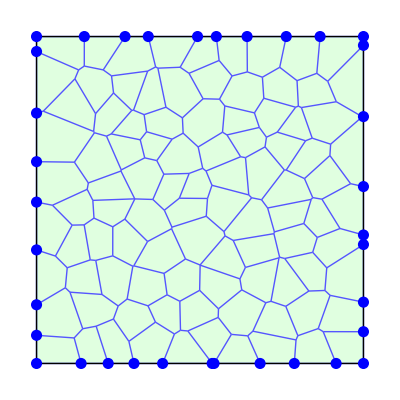

```mathematica
w=TemplateRandomSquareGrid[100, {0,0}, {15,15}];
vw=TissueVertices[w];
bvw=VerticesOnBoundary[w];
pictureOfPointsOnBoundary=Graphics[{Blue, PointSize[.02], Point[vw[[bvw]]]}];
Show[ShowTissue[w, "EdgeStyles"-> Lighter[Blue]], pictureOfPointsOnBoundary]
```

Convert the tissue to a torus for periodic boundary condition, and then display the matching vertices on the boundary

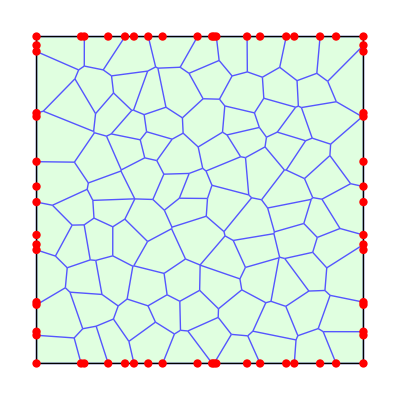

```mathematica
w1=ToTorus[w];
v=TissueVertices[w1];
bv=VerticesOnBoundary[TorusTissue[w1]];
pictureOfPointsOnBoundaryOfTorus=Graphics[{Red, PointSize[.015], Point[v[[bv]]]}];
Show[g=ShowTissue[w1, "EdgeStyles"-> Lighter[Blue]],pictureOfPointsOnBoundaryOfTorus ]
```

Draw a picture to demonstrate how the points on the boundary match up with edges on the opposite boundary

```mathematica
T=TorusTissue[w1];
ev=EdgeVertices[T];
v=TissueVertices[T];
bv=VerticesOnBoundary[T];
```

```mathematica
p=Graphics[{Blue, PointSize[.01], Point[v[[bv]]]}]; 
gc=Graphics[Line/@ev];
gr=Graphics[Translate[Line[#],{15,0}]&/@ev];
gb=Graphics[Translate[Line[#], {0,-15}]&/@ev];
gl=Graphics[Translate[Line[#], {-15,0}]&/@ev]; 
gt = Graphics[Translate[Line[#], {0, 15}]&/@ev];
```

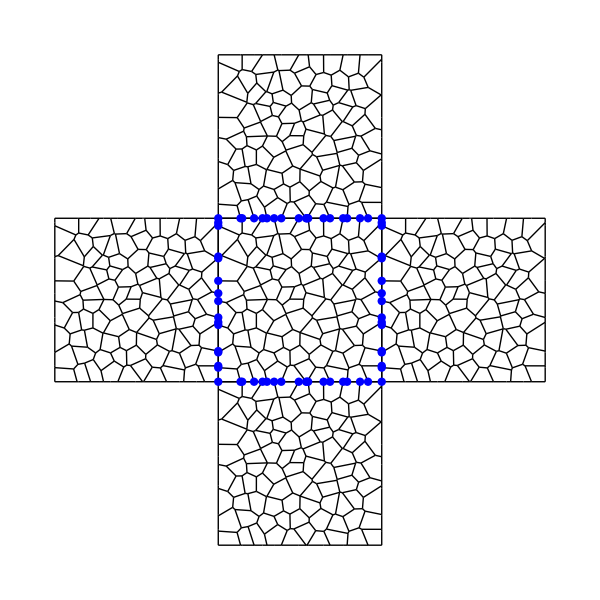

```mathematica
Show[{gc,gr, gb,gl,gt,  p}, ImageSize-> 600]
```

Define a network in a single cell

```mathematica
net={
{PZ↦X,hill[α1,n,K,0,1,α]},
{PX↦Y,hill[α1,n,K,0,1,α]},
{PY↦Z,hill[α1,n,K,0,1,α]},
{X⇄∅,k1,α0},{Y⇄∅,k1,α0},{Z⇄∅,k1,α0},{PX⇄∅,β,β*X[t]},{PY⇄∅,β,β*Y[t]},{PZ⇄∅,β,β*Z[t]}};
myrates={α->250,α0->0,α1->0,β->5,n->2.1,k1->1,K->1};
num=NTissueCells[w1]
```

95

```mathematica
bignet=CelleratorNetwork[w1, "Reactions"-> net, "Diffusion"-> {{PX, DPX}}];
```

95 Cells.

15 internal reactions in each cell.

1425 intracellular reactions.

568 diffusion reactions.

1993 total reactions.

Define random initial  conditions

```mathematica
myic=Flatten[{PX[#]-> RandomInteger[{0,100}], PY[#]-> RandomInteger[{0,25}], PZ[#]-> RandomInteger[{0,100}], X[#]-> 0, Y[#]-> 0, Z[#]-> 0}&/@Range[num]];
```

Run the simulation

```mathematica
sim=RunSim[bignet/.myrates, {DPX-> 2.5}, myic, {0,100}];
```

Plot species PX in all cells

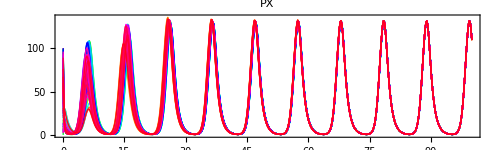

```mathematica
SimPlot[sim, PX, ImageSize-> 500, AspectRatio-> .3, "Points"-> 500]
```

Generate each frame in the movie

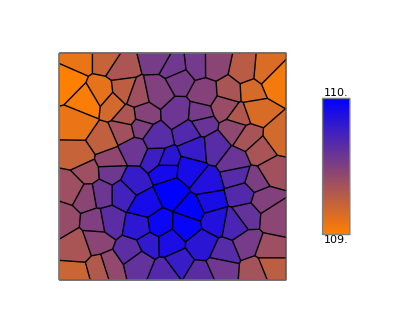

```mathematica
SimShowFinal[sim,PX, w, {Orange, Blue}]
```

```mathematica
m=SimAnimate[sim,PX, w, {0,100,.2}, {Orange, Blue}, {0,140}];
```

```mathematica
ListAnimate[m]
```

```mathematica
SaveFrames[m, "JPG",500,"NONE", "RepressilatorPeriodicBC"]
```

Created folder: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1019

Files will be in the folder: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1019

Created directory: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1019/Frames

Putting movie frames in  in /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1019/Frames

StringJoin::string: String expected at position 2 in ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3741370<>'.

ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3741370<>'

StringJoin::string: String expected at position 2 in 
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called <>Cellzilla2D`Private`moviefile$3741370<> and be in the same folder as all the frames..

ERROR: Unable to produce movie. ffmpeg return code is: 32512 On some versions of Mathematica (such as the version installed on this computer), the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd, change your current working directory to (e.g., with the cd command):
 cd /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1019
Then type the following:
ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3741370<>'
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called <>Cellzilla2D`Private`moviefile$3741370<> and be in the same folder as all the frames.

Repeat the simulation on the original tissue, but not as a torus, so there are no boundary conditions.

```mathematica
m=SimAnimate[sim,PX, w, {0,100, 50}, {Orange, Blue}, {0,140}];
```

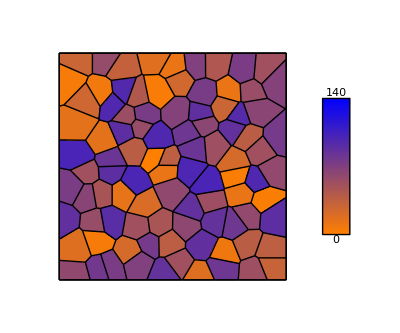
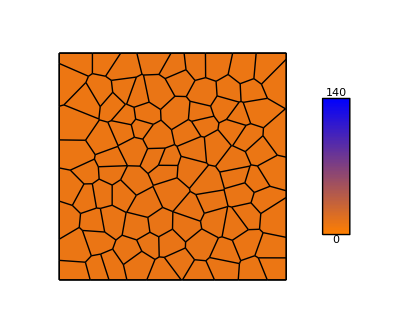
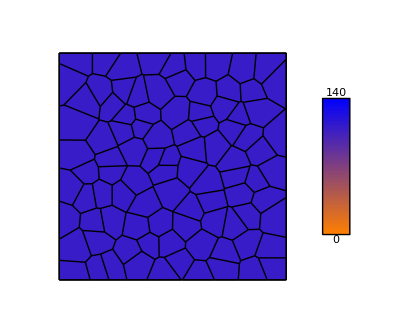

```mathematica
m
```

```mathematica
SaveFrames[m, "JPG",500,"NONE", "RepressilatorPeriodicBC"]
```

Created folder: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1036

Files will be in the folder: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1036

Created directory: /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1036/Frames

Putting movie frames in  in /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1036/Frames

StringJoin::string: String expected at position 2 in ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3976284<>'.

ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3976284<>'

StringJoin::string: String expected at position 2 in 
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called <>Cellzilla2D`Private`moviefile$3976284<> and be in the same folder as all the frames..

ERROR: Unable to produce movie. ffmpeg return code is: 32512 On some versions of Mathematica (such as the version installed on this computer), the Kernel is unable to locate the correct path execute ffmpeg. You must do this manually:

In a command shell such as bash, terminal, or cmd, change your current working directory to (e.g., with the cd command):
 cd /Users/mathman/Cellzilla/Simulations-18-Jun-17/RepressilatorPeriodicBC18Jun17-1036
Then type the following:
ffmpeg -r 16 -i 'FRAME%4d.JPG' '<>Cellzilla2D`Private`moviefile$3976284<>'
You can change the last field to whatever you want the movie to actually be called. In this case, it will be called <>Cellzilla2D`Private`moviefile$3976284<> and be in the same folder as all the frames.